```mathematica
Import["ToMatlab.m","Package"]
```

# Supporting Information Sec. 3.4 lattice mismatch base on -Graphics-

## AA stacking triangle Eq. S7

```mathematica
ClearAll["Global`*"]
```

```mathematica
$Assumptions=R>0&&r>0&&as>0&&0≤θ≤π/3&&p∈ Reals&&x∈Reals&&y∈Reals
```

```mathematica
fAA[x_,y_,λ_]=  Cos[(4 π (x))/(√3 λ)]+2 Cos[(2  π (x))/(√3 λ)] Cos[(2  π y)/λ]
```

Cos[(4 π x)/(√3 λ)]+2 Cos[(2 π x)/(√3 λ)] Cos[(2 π y)/λ]

```mathematica
Plot3D[fAA[x,y,1],{x,-1,1},{y,-1,1},AxesLabel->Automatic,ViewPoint->{0,0,Infinity}, ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
fAA[x_,y_,λ_]=fAA[x Cos[π/2]-y Sin[π/2],y Cos[π/2]+x Sin[π/2],λ] 
(*Rotate counter-clockwise*)
```

2 Cos[(2 π x)/λ] Cos[(2 π y)/(√3 λ)]+Cos[(4 π y)/(√3 λ)]

```mathematica
γ=ArcCos[(Cos[θ]-p)/Sqrt[1+p^2-2p Cos[θ]]]
```

ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]

```mathematica
β=γ-θ;
```

```mathematica
ftheta[x_,y_,λ_,θ_,p_]=fAA[x Cos[-β]-y Sin[-β],y Cos[-β]+x Sin[-β],λ]
```

Cos[(4 π (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)]+2 Cos[(2 π (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 λ)] Cos[(2 π (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/λ]

```mathematica
λ=p Rs/(1+p^2-2 p Cos[θ])^(1/2)
(*λ is the distance between AA domain*)
```

(p Rs)/(√(1+p^2-2 p Cos[θ]))

```mathematica
f0[x_,y_,Rs_,θ_,p_]=Simplify[ftheta[x,y,λ,θ,p]]
```

Cos[(4 π √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)]+2 Cos[(2 π √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)] Cos[(2 π √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(p Rs)]

```mathematica
nRf0[x_,y_,R_,Rs_,r_,θ_,p_]=Simplify[f0[x R,y R,Rs,θ,p] ]
```

Cos[(4 π R √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)]+2 Cos[(2 π R √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3 p Rs)] Cos[(2 π R √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(p Rs)]

```mathematica
nRnasnareauf0[x_,y_,θ_,r_,p_]=Simplify[nRf0[x,y,r*Rs*p,Rs,r,θ,p]]
```

Cos[(4 π r √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3)]+2 Cos[(2 π r √(1+p^2-2 p Cos[θ]) (y Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]+x Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]))/(√3)] Cos[2 π r √(1+p^2-2 p Cos[θ]) (x Cos[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]-y Sin[θ-ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])]

```mathematica
triarea=Integrate[Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}]
```

(3 √3)/4

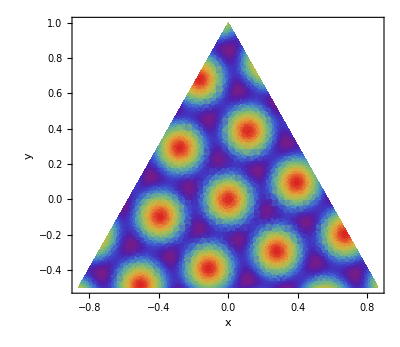

```mathematica
DensityPlot[nRnasnareauf0[x,y,4Degree,20Sqrt[3],2.46/2.504],{x,-1,1},{y,-1,1},AxesLabel->Automatic, ColorFunction->"Rainbow",MaxRecursion->3, PlotRange->All,RegionFunction->Function[{x,y,z},y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],AspectRatio->Automatic]
```

```mathematica
t1=AbsoluteTime[];
NEtri[theta_,r_,p_]=Simplify[Integrate[nRnasnareauf0[x,y,theta,r,p]Boole[y+Sqrt[3]x<1 &&y<Sqrt[3]x+1&& y>-1/2],{x,-1,1},{y,-1,1}] ];
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

time used 7.757461855 mins

```mathematica
t1=AbsoluteTime[];
AAtri[theta_,r_,p_]=FullSimplify[NEtri[theta,r,p]/triarea,r>0&&0≤theta&&p∈ Reals&&p>0&&r∈ Reals&&theta∈ Reals];
t2=AbsoluteTime[];
Print["time used ",(t2-t1)/60," mins"]
```

time used 201.38667272 mins

```mathematica
AAtri[θ,r,p]
```

(3 (2 Cos[(2 π r (Cos[θ] (-p+Cos[θ])+Abs[Sin[θ]] Sin[θ]))/(√3)] Cos[2 π r (Abs[Sin[θ]] Cos[θ]+(p-Cos[θ]) Sin[θ])]-2 Cos[(4 π r √(1+p^2-2 p Cos[θ]) Sin[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]+√3 Csc[1/2 (-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sec[1/2 (-θ+ArcCos[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[(2 π r (-p Cos[θ]+Cos[θ]^2+Abs[Sin[θ]] Sin[θ]))/(√3)] Sin[2 π r (Abs[Sin[θ]] Cos[θ]+(p-Cos[θ]) Sin[θ])]))/(4 π^2 r^2 (1+p^2-2 p Cos[θ]) (1-2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])]))

```mathematica
A[θ_,r_,p_]:=θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
B[θ_,r_,p_]:=-θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]
CC[θ_,r_,p_]:=2 π r √(1+p^2-2 p Cos[θ])
DD[θ_,r_,p_]:=4 π^2 r^2 (1+p^2-2 p Cos[θ]) (1-2 Cos[2A[θ,r,p]])
```

```mathematica
SumAAtri[θ_,r_,p_]=3/DD[θ,r,p](2Cos[CC[θ,r,p]]Cos[A[θ,r,p]]Cos[CC[θ,r,p] Sin[A[θ,r,p]]/(√3)]-2Cos[2CC[θ,r,p] Sin[A[θ,r,p]]/(√3)]+√3 Csc[1/2 B[θ,r,p]]Sec[1/2 B[θ,r,p]]Sin[A[θ,r,p]]Sin[CC[θ,r,p]Cos[A[θ,r,p]]]Sin[2CC[θ,r,p] Sin[A[θ,r,p]]/(√3)])
```

-((3 (2 Cos[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Cos[2 π r √(1+p^2-2 p Cos[θ])] Cos[(2 π r √(1+p^2-2 p Cos[θ]) Sin[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]-2 Cos[(4 π r √(1+p^2-2 p Cos[θ]) Sin[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]+√3 Csc[1/2 (-θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sec[1/2 (-θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])] Sin[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]] Sin[2 π r √(1+p^2-2 p Cos[θ]) Cos[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]]] Sin[(4 π r √(1+p^2-2 p Cos[θ]) Sin[θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))]])/(√3)]))/(4 π^2 r^2 (1+p^2-2 p Cos[θ]) (1-2 Cos[2 (θ+ArcSin[(-p+Cos[θ])/(√(1+p^2-2 p Cos[θ]))])])))

```mathematica
ToMatlab[AAtri[theta,r,p]]
```

(3/4).*pi.^(-2).*r.^(-2).*(1+p.^2+(-2).*p.*cos(theta)).^(-1).*(1+( ...
  -2).*cos(2.*(theta+asin(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.* ...
  cos(theta)).^(-1/2))))).^(-1).*(2.*cos(2.*3.^(-1/2).*pi.*r.*(cos( ...
  theta).*((-1).*p+cos(theta))+abs(sin(theta)).*sin(theta))).*cos( ...
  2.*pi.*r.*(abs(sin(theta)).*cos(theta)+(p+(-1).*cos(theta)).*sin( ...
  theta)))+(-2).*cos(4.*3.^(-1/2).*pi.*r.*(1+p.^2+(-2).*p.*cos( ...
  theta)).^(1/2).*sin(theta+asin(((-1).*p+cos(theta)).*(1+p.^2+(-2) ...
  .*p.*cos(theta)).^(-1/2))))+3.^(1/2).*csc((1/2).*((-1).*theta+ ...
  acos(((-1).*p+cos(theta)).*(1+p.^2+(-2).*p.*cos(theta)).^(-1/2)))) ...
  .*sec((1/2).*((-1).*theta+acos(((-1).*p+cos(theta)).*(1+p.^2+(-2) ...
  .*p.*cos(theta)).^(-1/2)))).*sin(theta+asin(((-1).*p+cos(theta)).* ...
  (1+p.^2+(-2).*p.*cos(theta)).^(-1/2))).*sin(2.*3.^(-1/2).*pi.*r.*( ...
  (-1).*p.*cos(theta)+cos(theta).^2+abs(sin(theta)).*sin(theta))).* ...
  sin(2.*pi.*r.*(abs(sin(theta)).*cos(theta)+(p+(-1).*cos(theta)).* ...
  sin(theta))));